# Типовой расчет

Михалькевич Д.Н.
гр. 221701

Вариант 8

```mathematica
table=({{0.50, 0.443179}, {0.56, 0.469718}, {0.62, 0.509651}, {0.68, 0.523462}, {0.74, 0.551931}, {0.8, 0.551792}, {0.86, 0.566707}, {0.92, 0.551781}, {0.98, 0.551341}, {1.04, 0.521204}, {1.1, 0.503945}, {1.16, 0.458602}, {1.22, 0.42344}, {1.28, 0.363326}, {1.34, 0.309594}, {1.4, 0.235574}, {1.46, 0.163046}, {1.52, 0.0764054}, {1.58, -0.014687}, {1.64, -0.112269}, {1.7, -0.221226}, {1.76, -0.327705}, {1.82, -0.45336}, {1.88, -0.566363}, {1.94, -0.707094}, {2, -0.823971}});a=0.5;b=2;h=0.06;dots = (b-a)/h+1;
data= Table[{table[[i,1]],table[[i,2]]}, {i,1,dots}];
f=Fit[data,{1,x,x^2},x]
```

-0.190028+1.78112 x-1.05464 x^2

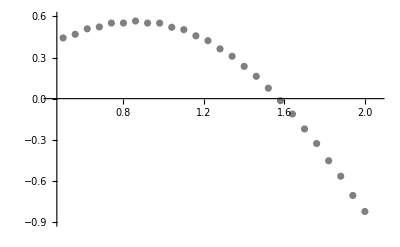

```mathematica
Show[ListPlot[table,PlotStyle->Gray,PlotLabels->Automatic],PlotRange->{{a-h,b+h},{-0.9,0.6}}]
```

## Задание 1.

### Постройте для функции f(x) интерполяционный многочлен степени n=25 и многочлены меньшей степени на отрезке, используя не все узлы сетки: - используете значения функции в нечетных узлах (n=12); - используете значения функции в каждом 3- узле (n=8); - используете значения функции в каждом 5- узле (n=5). Выведите графики интерполяционных многочленов и оцените их поведение на отрезке. Сравните результаты и сделайте выводы о зависимость погрешности интерполирования от числа узлов.

#### Построение многочлена степенью 25 :

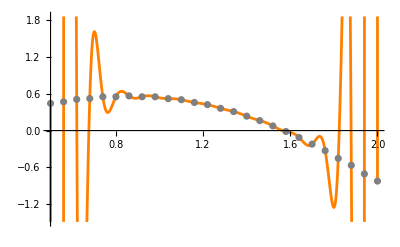

```mathematica
Poly25 = InterpolatingPolynomial[data,x];
Plot25 = Plot[Poly25, {x,a,b}, PlotStyle->{Orange}];
Dots25 = ListPlot[data,PlotStyle->Gray];
Show[Plot25,Dots25]
```

```mathematica
(*Найдём абсолютную погрешность многочлена в заданных точках*)
```

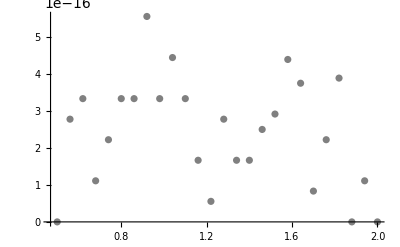

```mathematica
Diff25=
Table[{data[[i,1]],(Poly25/.x->data[[i,1]])-data[[i,2]]},{i,1,dots}];
Show[ListPlot[Diff25,PlotStyle->Gray]]
```

```mathematica
Sum[((Poly25/.x->data[[i,1]])-data[[i,2]])^2, {i,dots}]
```

2.06193×10^-30

#### Используя значения функции в нечетных узлах:

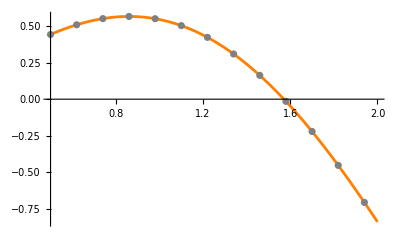

```mathematica
data12 = Table[{data[[i,1]],data[[i,2]]},{i,1,26,2}];
Poly12 = InterpolatingPolynomial[data12, x];
plot12 = Plot[Poly12, {x,a,b}, PlotStyle->Orange];
dots12=ListPlot[data12, PlotStyle->Gray];Show[plot12,dots12]
```

```mathematica
(*Найдём абсолютную погрешность многочлена в заданных точках*)
```

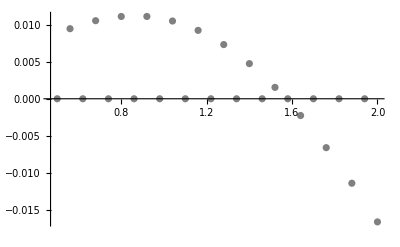

```mathematica
Diff12=
Table[{data[[i,1]],(Poly12/.x->data[[i,1]])-data[[i,2]]},{i,1,dots}];
Show[ListPlot[Diff12,PlotStyle->Gray]]
```

```mathematica
Sum[((Poly12/.x->data[[i,1]])-data[[i,2]])^2, {i,dots}]
```

0.00118394

#### Используя значения функции в каждом третьем узле:

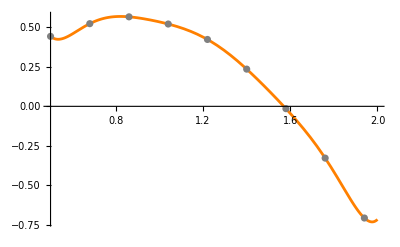

```mathematica
data8 = Table[{data[[i,1]],data[[i,2]]},{i,1,26,3}];
Poly8 = InterpolatingPolynomial[data8, x];
plot8 = Plot[Poly8, {x,a,b}, PlotStyle->Orange];
dots8=ListPlot[data8, PlotStyle->Gray];Show[plot8,dots8]
```

```mathematica
(*Найдём абсолютную погрешность многочлена в заданных точках*)
```

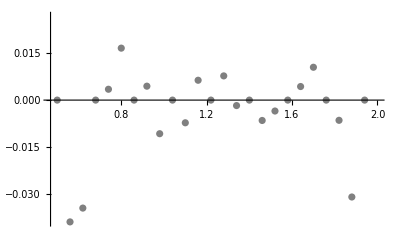

```mathematica
Diff8=
Table[{data[[i,1]],(Poly8/.x->data[[i,1]])-data[[i,2]]},{i,1,dots}];
Show[ListPlot[Diff8,PlotStyle->Gray]]
```

```mathematica
Sum[((Poly8/.x->data[[i,1]])-data[[i,2]])^2, {i,dots}]
```

0.0160538

#### Используя значения функции в каждом пятом узле:

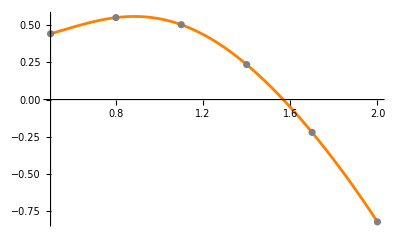

```mathematica
data5 = Table[{data[[i,1]],data[[i,2]]},{i,1,26,5}];
Poly5 = InterpolatingPolynomial[data5, x];
plot5 = Plot[Poly5, {x,a,b}, PlotStyle->Orange];
dots5=ListPlot[data5, PlotStyle->Gray];Show[plot5,dots5]
```

```mathematica
(*Найдём абсолютную погрешность многочлена в заданных точках*)
```

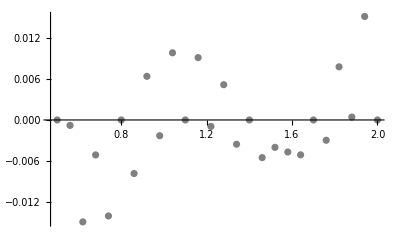

```mathematica
Diff5=
Table[{data[[i,1]],(Poly5/.x->data[[i,1]])-data[[i,2]]},{i,1,dots}];
Show[ListPlot[Diff5,PlotStyle->Gray]]
```

```mathematica
Sum[((Poly5/.x->data[[i,1]])-data[[i,2]])^2, {i,dots}]
```

0.00116817

#### Вывод: наилучшим в сравнении по сумме квадратов разностей функции в заданных узлах оказался многочлен 25-й степени. По графикам можно заметить, что погрешность увеличивается ближе к крайним значениям интерполируемой функции. Но несмотря на это, интерполяция не гарантирует, что поведение полученной функции между узлами интерполяции будет повторять поведение исходной функции (погрешность увеличивается в узлах, которые не были выбраны для интерполяции 5, 8 и 12 степеней).

## Задание 2.

### Постройте сплайны, аппроксимирующие функцию f(x) по значениям в узлах, выведите графики и сравните с графиками интерполяционных многочленов степени n = 5, 8, 12, 25, построенных по тем же узлам.

#### Построим аппроксимирующий сплайн заданного многочлена 5 степени

```mathematica
Spline5:=Interpolation[data5,x,Method->"Spline"]
SplinePlot5 = Plot[Spline5, {x,a,b}, PlotStyle->{Orange}];
```

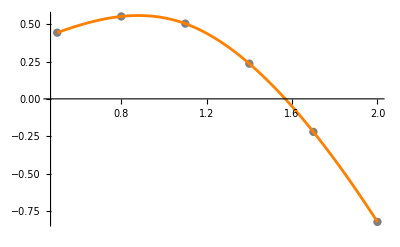

```mathematica
Show[ListPlot[data5, PlotStyle->{PointSize[0.015],Gray}],SplinePlot5]
```

```mathematica
Sum[((Spline5/.x->data[[i,1]])-data[[i,2]])^2, {i,dots}]
```

0.000908471

#### Построим аппроксимирующий сплайн заданного многочлена 8 степени

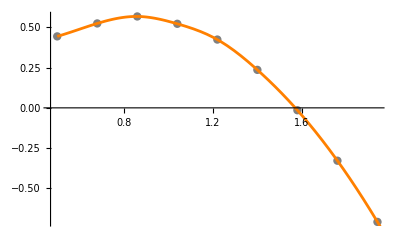

```mathematica
Spline8:=Interpolation[data8,x,Method->"Spline"]
SplinePlot8 = Plot[Spline8, {x,a,b}, PlotStyle->{Orange}];
Show[ListPlot[data8, PlotStyle->{PointSize[0.015],Gray}],SplinePlot8]
```

```mathematica
Sum[((Spline8/.x->data[[i,1]])-data[[i,2]])^2, {i,dots}]
```

0.00132162

#### Построим аппроксимирующий сплайн заданного многочлена 12 степени

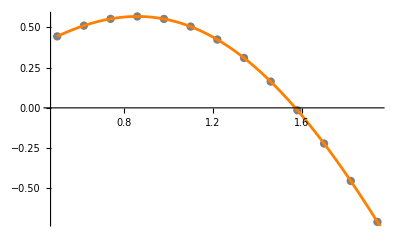

```mathematica
Spline12:=Interpolation[data12,x,Method->"Spline"]
SplinePlot12 = Plot[Spline12, {x,a,b}, PlotStyle->{Orange}];
Show[ListPlot[data12, PlotStyle->{PointSize[0.015],Gray}],SplinePlot12]
```

```mathematica
Sum[((Spline12/.x->data[[i,1]])-data[[i,2]])^2, {i,dots}]
```

0.00118744

#### Построим аппроксимирующий сплайн заданного многочлена 25 степени

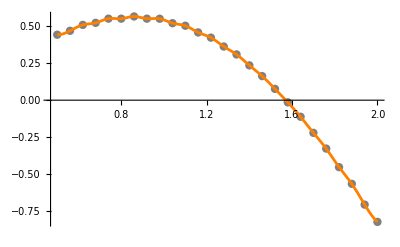

```mathematica
Spline25:=Interpolation[data,x,Method->"Spline"]
SplinePlot25 = Plot[Spline25, {x,a,b}, PlotStyle->{Orange}];
Show[ListPlot[data, PlotStyle->{PointSize[0.015],Gray}],SplinePlot25]
```

```mathematica
Sum[((Spline25/.x->data[[i,1]])-data[[i,2]])^2, {i,dots}]
```

5.95233×10^-32

#### Вывод: наилучшим в сравнении по сумме квадратов разностей функции в заданных узлах оказался сплайн 25-й степени . Погрешность оказалась меньше, чем в случае интерполяционного многочлена из Задания 1.

## Задание 3.

### Постройте для функции f(x) многочлены наилучшего cреднеквадратичного приближения Pn*(x) степени n = 1,2. Вычислите для каждого многочлена сумму квадратов отклонения в узлах, сравните их значения и сделайте выводы. Выведите графики узлов и многочленов Pn*(x), аппроксимирующих функцию.

```mathematica
Subscript[P, 1]=Fit[data,{1,x},x];
Subscript[P, 2]=Fit[data,{1,x, x^2},x];
```

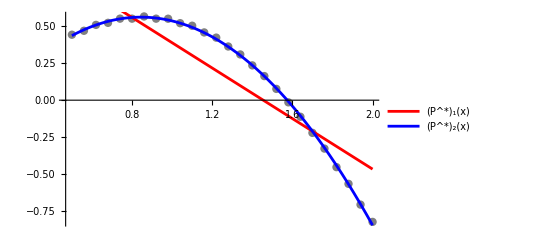

```mathematica
PPlot = Plot[{Subscript[P, 1],Subscript[P, 2]}, {x,a,b},PlotStyle->{Red, Blue}, PlotLegends->{"(P^*)_1(x)","(P^*)_2(x)"}];
Show[ListPlot[data, PlotStyle->{PointSize[0.015],Gray}],PPlot]
```

```mathematica
Sum[((Subscript[P, 1]/.x->data[[i,1]])-data[[i,2]])^2, {i,dots}]
```

0.946032

```mathematica
Sum[((Subscript[P, 2]/.x->data[[i,1]])-data[[i,2]])^2, {i,dots}]
```

0.00155621

#### Вывод: многочлен наилучшего cреднеквадратичного приближения второго порядка показал лучшую точность графически и исходя из высчитанной суммы квадратов разностей.

## Задание 4.

### Вычислите определенный интеграл следующими методами : -методами левых, правых и средних прямоугольников; -методом трапеций; -методом парабол (Симпсона). Сравните полученные приближенные значения интеграла и сделайте выводы о точности результата.

```mathematica
(*метод левых прямоугольников*)
LeftS=h*∑_(i=1)^(dots-1) data[[i,2]]
```

0.32232

```mathematica
(*метод правых прямоугольников*)
RightS=h*∑_(i=2)^(dots-1) data[[i,2]]
```

0.295729

```mathematica
(*метод средних прямоугольников*)
MiddleS=h*∑_(i=1)^(dots-1) (data[[i,2]]+data[[i+1,2]])/2
```

0.284305

```mathematica
(*Метод трапеций*)
```

```mathematica
TrapezoidMethod=h*((data[[1,2]]+data[[2,2]])/2+∑_(i=3)^(dots-2) data[[i,2]])
```

0.337358

```mathematica
(*Метод парабол*)
```

```mathematica
n = 12;
h = (b-a)/(2n);
For[i=0,i<=2*n,i++, Subscript[y, i]=data[[i+1,2]];]
SimpsonFormula=∑_(i=0)^(n-1) h/3*(Subscript[y, 2i]+4 Subscript[y, 2i+1]+Subscript[y, 2i+2])
```

0.343728

#### Вывод: Методы средних треугольников, трапеций и парабол позволяют получить более точный результат.

## Задание 5.

### Постройте с помощью формул численного дифференцирования первого и второго порядка точности таблицу первых и вторых производных функции f (x) в узлах сетки. Сравните полученные результаты и сделайте выводы.

```mathematica
(*Первый уровень точности первой производной*)
```

```mathematica
FirstT=Table[{i,data[[i,1]],(data[[i+1,2]]-data[[i,2]])/h},{i,1,dots-1}];
TableForm[FirstT,TableHeadings->{None,{"Node","x_i","y'_i"}} ]
```

Node | x_i | y'_i
1 | 0.5 | 0.424624
2 | 0.56 | 0.638928
3 | 0.62 | 0.220976
4 | 0.68 | 0.455504
5 | 0.74 | -0.002224
6 | 0.8 | 0.23864
7 | 0.86 | -0.238816
8 | 0.92 | -0.00704
9 | 0.98 | -0.482192
10 | 1.04 | -0.276144
11 | 1.1 | -0.725488
12 | 1.16 | -0.562592
13 | 1.22 | -0.961824
14 | 1.28 | -0.859712
15 | 1.34 | -1.18432
16 | 1.4 | -1.16045
17 | 1.46 | -1.38625
18 | 1.52 | -1.45748
19 | 1.58 | -1.56131
20 | 1.64 | -1.74331
21 | 1.7 | -1.70366
22 | 1.76 | -2.01048
23 | 1.82 | -1.80805
24 | 1.88 | -2.2517
25 | 1.94 | -1.87003

```mathematica
(*Второй уровень точности первой и второй производной*)
```

```mathematica
FirstT=Table[{i,data[[i,1]],(data[[i+1,2]]-data[[i-1,2]])/(2*h)},{i,2,dots-1}];
SecondT= Table[{(data[[i+1,2]]-2*data[[i,2]]+data[[i-1,2]])/h^2},{i,2,dots-1}]; (*Для второй производной уровни точности идут со второго и только четные*)
tab = Join[FirstT,SecondT,2];
TableForm[tab,TableHeadings->{None,{"Node","x_i","y'_i","y('')_i"}} ]
```

Node | x_i | y'_i | y('')_i
2 | 0.56 | 0.531776 | 3.42886
3 | 0.62 | 0.429952 | -6.68723
4 | 0.68 | 0.33824 | 3.75245
5 | 0.74 | 0.22664 | -7.32365
6 | 0.8 | 0.118208 | 3.85382
7 | 0.86 | -0.000088 | -7.6393
8 | 0.92 | -0.122928 | 3.70842
9 | 0.98 | -0.244616 | -7.60243
10 | 1.04 | -0.379168 | 3.29677
11 | 1.1 | -0.500816 | -7.1895
12 | 1.16 | -0.64404 | 2.60634
13 | 1.22 | -0.762208 | -6.38771
14 | 1.28 | -0.910768 | 1.63379
15 | 1.34 | -1.02202 | -5.19373
16 | 1.4 | -1.17238 | 0.381952
17 | 1.46 | -1.27335 | -3.61283
18 | 1.52 | -1.42186 | -1.13966
19 | 1.58 | -1.5094 | -1.66134
20 | 1.64 | -1.65231 | -2.912
21 | 1.7 | -1.72349 | 0.634368
22 | 1.76 | -1.85707 | -4.90906
23 | 1.82 | -1.90926 | 3.23891
24 | 1.88 | -2.02987 | -7.09837
25 | 1.94 | -2.06086 | 6.10662

#### Вывод : мы можем получить удовлетворительные результаты при нахождении производных 1 и 2 порядка . Однако при шаге сетки, близком к нулю, неустранимые погрешности в значениях функции оказывают сильное влияние на результат, о чём свидетельствуют вычисленные значения 2 ой производной .